```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"velocity tools","init.nb"}]];
```

#### Scenario 1: Exact Equation Derivation

My derivation based on the concept of a hyperplane slicing a cone in the slip-linearized region.

```mathematica
First@Timing@Quiet@defVel[F0,0.5{Cos[t],Sin[t]}]
First@Timing@Quiet@defVel[F1,4{Cos[t],Sin[t]}]
```

0.0625

0.109375

```mathematica
(* minimum x coordinate of -F1^° *)
{ζ1xMin,ζ1xMinRule}=Minimize[{-(F1^°)_bdryParam[[1]],-π≤t<π},t]
vsPlus=(𝒩̂)_(F1^°)@(F1^°)_bdryParam/.ζ1xMinRule
(* find normal vectors of F0 with the x coordinate -ζ1xMin -- only possible if entering faster region *)
{-ζ1xMin,#}&/@Last/@First/@Solve[(F0^°)_bdryCnds,{y},Reals]/.{x->-ζ1xMin}
(* select the vector that is pointing upwards and find it's corresponding velocity *)
{vcPlus}=(𝒩̂)_(F0^°)/@Select[%,NonNegative@Last@#&]
```

{-1/4,{t→0}}

{4,0}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{1/4,-1.98431},{1/4,1.98431}}

{{0.0625,0.496078}}

```mathematica
x0={0,-1};
(* yc occurs at the time when x0 + t vcPlus has a zero y component *)
tc=-x0⟦2⟧/vcPlus⟦2⟧
yc=x0+tc vcPlus
```

2.01581

{0.125988,-1.11022×10^-16}

```mathematica
vcPlusReflected={{1,0},{0,-1}}.vcPlus
```

{0.0625,-0.496078}

{0.125988,-1.11022×10^-16,2.01581}

{0.188488,-0.496078,3.01581}

{4.12599,-1.11022×10^-16,3.01581}

0.503953 (3.9375+0.496078 x-3.9375 y)

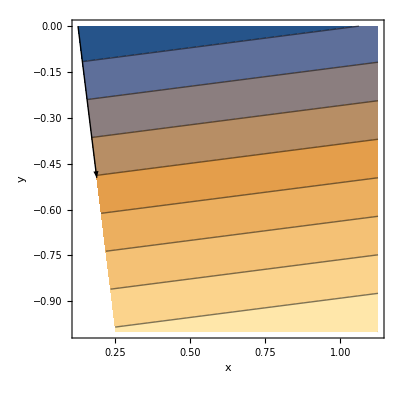

```mathematica
R1=ImplicitRegion[y≤0&&{x,y}.(ℛ[-π/2].vcPlusReflected)≤yc.(ℛ[-π/2].vcPlusReflected),{x,y}];
(* define plane by 3 points, z component is time *)
p1=yc~Append~tc
p2=(vcPlusReflected+yc)~Append~(tc+1)
p3=(vsPlus+yc)~Append~(tc+1)
(* The matrix {{x,1},{Subscript[p, 1],1},,{Subscript[p, n],1}} will be singular when x is coplanar with each Subscript[p, i]. 1's column included for constant term. *)
planeEqu=z/.Solve[Det[({{x,y,z},p1,p2,p3}ᵀ~Append~{1,1,1,1})ᵀ]==0,z][[1]]
Show[{
ContourPlot[planeEqu,{x,y}∈R1,FrameLabel->{x,y}],
Graphics[{Thick,Arrow[{yc,yc+vcPlusReflected}]}]
}]
```

```mathematica
z/.Solve[Det[({{x,y,z},{x1,y1,z1},{x2,y2,z2},{x3,y3,z3}}ᵀ~Append~{1,1,1,1})ᵀ]==0,z][[1]]//FullSimplify
Collect[Numerator@%,{x,y}]
```

(-x2 y z1+x3 y z1+x y2 z1-x3 y2 z1-x y3 z1+x2 y3 z1+x1 y z2-x3 y z2-x y1 z2+x3 y1 z2+x y3 z2-x1 y3 z2+(x2 (y-y1)+x (y1-y2)+x1 (-y+y2)) z3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))

-x3 y2 z1+x2 y3 z1+x3 y1 z2-x1 y3 z2-x2 y1 z3+x1 y2 z3+y (-x2 z1+x3 z1+x1 z2-x3 z2-x1 z3+x2 z3)+x (y2 z1-y3 z1-y1 z2+y3 z2+(y1-y2) z3)

```mathematica
(* gives equation for z in terms of {x,y} for a plane that contains 3 points *)
PlaneThroughPointsZ[{x1_,y1_,z1_},{x2_,y2_,z2_},{x3_,y3_,z3_}]:=(-x3 y2 z1+x2 y3 z1+x3 y1 z2-x1 y3 z2-x2 y1 z3+x1 y2 z3+y (-x2 z1+x3 z1+x1 z2-x3 z2-x1 z3+x2 z3)+x (y2 z1-y3 z1-y1 z2+y3 z2+(y1-y2) z3))/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))//Cancel
```

The picture below shows how the full gauge for reflected paths may be defined as a piecewise function over 3 regions in ℳ_0.

-Graphics-

#### SingleSourceReflectedGauge Function

```mathematica
SingleSourceReflectedGauge[x0_,F0_,F1_]:=Module[{x0Reflected,
ζ1xMin,ζ1xMinRule,vcPlus,vcPlusReflected,tcPlus,ycPlus,vsPlus,planeEquPlus,
ζ1xMax,ζ1xMaxRule,vcMinus,vcMinusReflected,tcMinus,ycMinus,vsMinus,planeEquMinus},
(* Todo: Generalize to highway problem solution. *)
x0Reflected={{1,0},{0,-1}}.x0;

{ζ1xMin,ζ1xMinRule}=Minimize[{-(F1^°)_bdryParam[[1]],-π≤t<π},t];
vsPlus=(𝒩̂)_(F1^°)@(F1^°)_bdryParam/.ζ1xMinRule;
{vcPlus}=(𝒩̂)_(F0^°)/@Select[
{-ζ1xMin,#}&/@Last/@First/@Solve[N@(F0^°)_bdryCnds,{y},Reals]/.{x->-ζ1xMin},
NonNegative@Last@#&];
vcPlusReflected={{1,0},{0,-1}}.vcPlus;
tcPlus=-x0⟦2⟧/vcPlus⟦2⟧;
ycPlus=x0+tcPlus vcPlus;
planeEquPlus=PlaneThroughPointsZ[ycPlus~Append~tcPlus,(vcPlusReflected+ycPlus)~Append~(tcPlus+1),(vsPlus+ycPlus)~Append~(tcPlus+1)];

{ζ1xMax,ζ1xMaxRule}=Maximize[{-(F1^°)_bdryParam[[1]],-π≤t<π},t];
vsMinus=(𝒩̂)_(F1^°)@(F1^°)_bdryParam/.ζ1xMaxRule;
{vcMinus}=(𝒩̂)_(F0^°)/@Select[
{-ζ1xMax,#}&/@Last/@First/@Solve[N@(F0^°)_bdryCnds,{y},Reals]/.{x->-ζ1xMax},
NonNegative@Last@#&];
vcMinusReflected={{1,0},{0,-1}}.vcMinus;
tcMinus=-x0⟦2⟧/vcMinus⟦2⟧;
ycMinus=x0+tcMinus vcMinus;
planeEquMinus=PlaneThroughPointsZ[ycMinus~Append~tcMinus,(vcMinusReflected+ycMinus)~Append~(tcMinus+1),(vsMinus+ycMinus)~Append~(tcMinus+1)];

Piecewise[{{planeEquPlus, y≤0&&{x,y}.(ℛ[-π/2].vcPlusReflected)≤ycPlus.(ℛ[-π/2].vcPlusReflected)}, {planeEquMinus, y≤0&&{x,y}.(ℛ[π/2].vcMinusReflected)≤ycMinus.(ℛ[π/2].vcMinusReflected)}, {Subscript[γ, F0][{x,y}-x0Reflected], y≤0&&{x,y}.(ℛ[π/2].vcPlusReflected)<ycPlus.(ℛ[π/2].vcPlusReflected)&&{x,y}.(ℛ[-π/2].vcMinusReflected)<ycMinus.(ℛ[-π/2].vcMinusReflected)}, {Infinity, True}}]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Piecewise[{{0.5 (3.87298+1. x-3.87298 y), y≤0&&-0.484123 x-0.125 y≤-0.125}, {-0.5 (-3.87298+1. x+3.87298 y), y≤0&&0.484123 x-0.125 y≤-0.125}, {2. √(x^2+(-1+y)^2), y≤0&&0.484123 x+0.125 y<0.125&&-0.484123 x+0.125 y<0.125}, {∞, True}}]

-Graphics3D-

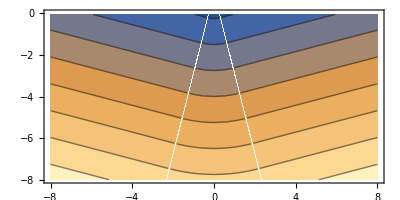

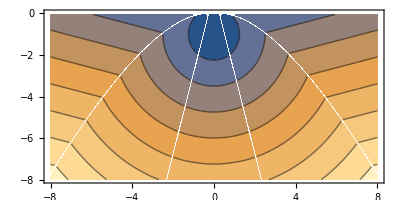

```mathematica
Quiet@defVel[F0,0.5{Cos[t],Sin[t]}]
Quiet@defVel[F1,2{Cos[t],Sin[t]}]
x0={0,-1};

SingleSourceReflectedGauge[x0,F0,F1]
Plot3D[{Subscript[γ, F0][{x,y}-x0],%,Min[Subscript[γ, F0][{x,y}-x0],%]},{x,-4,4},{y,-4,0},AxesLabel->{x,y,z},PlotStyle->{Transparent,Transparent,ColorData[97][1]}]
ContourPlot[%%,{x,-8,8},{y,-8,0},AspectRatio->{1,1}]
ContourPlot[Min[Subscript[γ, F0][{x,y}-x0],%%%],{x,-8,8},{y,-8,0},AspectRatio->{1,1}]
```

```mathematica
Γ0=Subscript[γ, F0][{x,y}-x0];(* single-media problem *)
Γ010=SingleSourceReflectedGauge[x0,F0,F1];(* specific highway problem *)
GraphicsRow[{
ContourPlot[Γ0,{x,-8,8},{y,-8,0},AspectRatio->{1,1},Contours->Range[20],PlotLabel->"Γ(#, x0)& for 𝒫_(0)"],
ContourPlot[Γ010,{x,-8,8},{y,-8,0},AspectRatio->{1,1},Contours->Range[20],PlotLabel->"Γ(#, x0)& for 𝒫_(0, 1, 0)"]
},ImageSize->Large,AspectRatio->1/2]
```

Set::shape: Lists {ζ1xMin$26620,ζ1xMinRule$26620} and Minimize[{-Cos[t]/b,-π≤t<π},t] are not the same shape.

ReplaceAll::reps: {ζ1xMinRule$26620} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Set::shape: Lists {vcPlus$26620} and {} are not the same shape.

Part::partd: Part specification x0⟦2⟧ is longer than depth of object.

Part::partd: Part specification vcPlus$26620⟦2⟧ is longer than depth of object.

Set::shape: Lists {ζ1xMax$26620,ζ1xMaxRule$26620} and Maximize[{-Cos[t]/b,-π≤t<π},t] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

ReplaceAll::reps: {ζ1xMaxRule$26620} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partd: Part specification x0⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {ζ1xMinRule$26620} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ζ1xMaxRule$26620} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ζ1xMinRule$26620} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Piecewise[{{1.93649-0.5 x, x≤-0.258199}, {1.93649+0.5 x, x≥0.258199}, {2. √(1+x^2), True}}]

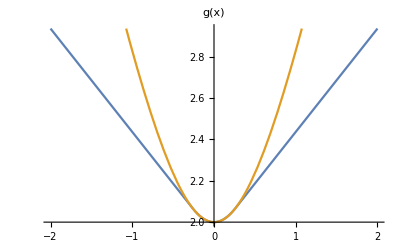

Piecewise[{{-0.5, x<-0.258199}, {(2. x)/(√(1.+x^2)), -0.258199<x<0.258199}, {0.5, x>0.258199}, {Indeterminate, True}}]

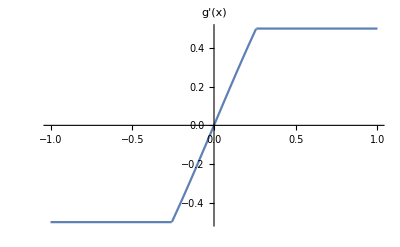

```mathematica
(* plot slice of gauge along interface *)
SingleSourceReflectedGauge[x0,F0,F1]/.y->0//Simplify
Plot[{%,Subscript[γ, F0][{x,0}-x0]},{x,-2,2},PlotRange->{%/.x->0,%/.x->2},PlotLabel->"g(x)"]
(* clips derivative of gauge to 1/v2 *)
∂_x %%//N
Plot[%,{x,-1,1},PlotLabel->"g'(x)"]
```

```mathematica
First@Timing@Quiet@defVel[F0,a{Cos[t],Sin[t]}]
First@Timing@Quiet@defVel[F1,b{Cos[t],Sin[t]}]
```

0.421875

0.5

```mathematica
((F0^°)_bdryParam[[2]]/.t->t1)==((F1^°)_bdryParam[[2]]/.t->t2)
```

Sin[t1]/a==Sin[t2]/b

#### General Equation: Circle F_0

Pure derivation of bifurcation line for F_0=aℬ and F_1=bℬ with b>a>0. Generalizes to the case where F_0=aℬ, b=max(proj_T_Σ(F_1)), and x_0=(0,-d)ᵀ.

```mathematica
First@Timing@Quiet@defVel[F0,a{Cos[t],Sin[t]}]
First@Timing@Quiet@defVel[F1,b{Cos[t],Sin[t]}]
lenAssumptions=b>a>0&&d>0;
```

0.109375

0.15625

```mathematica
-(F1^°)_bdryParam[[1]]
```

-Cos[t]/b

```mathematica
ζ1xMin=-1/b;
vsPlus={b,0};
```

```mathematica
(F0^°)_bdryCnds
#^2&/@%//Simplify
```

Max[-a √(x^2+y^2),a √(x^2+y^2)]==1

a^2 (x^2+y^2)==1

```mathematica
vcPlus=Simplify[(𝒩̂)_(F0^°)[{1/b,√(1/a^2-(1/b)^2)}],lenAssumptions]
vcPlusReflected={{1,0},{0,-1}}.vcPlus;
```

```mathematica
Total[#^2&/@{a^2/b,(a √(-a^2+b^2))/b}]//FullSimplify
```

a^2

```mathematica
x0={0,-d};
tc=-x0⟦2⟧/vcPlus⟦2⟧
yc=x0+tc vcPlus
planeEqu=PlaneThroughPointsZ[yc~Append~tc,(vcPlusReflected+yc)~Append~(tc+1),(vsPlus+yc)~Append~(tc+1)]
```

(b d)/(a √(-a^2+b^2))

{(a d)/(√(-a^2+b^2)),0}

(-a^2 d+b^2 d+a √(-a^2+b^2) x+a^2 y-b^2 y)/(a b √(-a^2+b^2))

```mathematica
{yc~Append~tc,(vsPlus+yc)~Append~(tc+1),(vcPlusReflected+yc)~Append~(tc+1)}//Simplify//ColumnForm
```

{(a d)/(√(-a^2+b^2)),0,(b d)/(a √(-a^2+b^2))}
{b+(a d)/(√(-a^2+b^2)),0,1+(b d)/(a √(-a^2+b^2))}
{a (a/b+d/(√(-a^2+b^2))),-(a √(-a^2+b^2))/b,1+(b d)/(a √(-a^2+b^2))}

```mathematica
regAssumtions=y≤0&&{x,y}.(ℛ[-π/2].vcPlusReflected)≤yc.(ℛ[-π/2].vcPlusReflected);
(* the equation that implicitly defines the plane-cone intersection *)
equ=Simplify[Subscript[γ, F0][{x,y}-x0]==planeEqu,
lenAssumptions&&regAssumtions]
```

b^2 d+a (√(-a^2+b^2) x+a y)==a^2 d+b^2 y+b √((-a^2+b^2) (x^2+(d+y)^2))

```mathematica
FullSimplify[Collect[Solve[equ,y],x],
lenAssumptions&&regAssumtions]
Manipulate[
Plot[y/.%,{x,0,50}]
,{{b,1.5},1,4},{{a,0.5},0,b},{d,1,3}]
```

{{y→d-(√(-a^2+b^2) x)/a-(2 b (b d+√(d (-a^2 d+b^2 d+a √(-a^2+b^2) x))))/a^2},{y→d-(√(-a^2+b^2) x)/a+(2 b (-b d+√(d (-a^2 d+b^2 d+a √(-a^2+b^2) x))))/a^2}}

The lower curve is not in the feasible region for paths that travel the interface.

```mathematica
Reduce[y==d-(√(-a^2+b^2) x)/a-(2 b (b d+√(d (-a^2 d+b^2 d+a √(-a^2+b^2) x))))/a^2&&lenAssumptions&&regAssumtions]
```

False

Therefore the upper curve gives us an equation for the bifurcation.

```mathematica
Simplify[Limit[d-(√(-a^2+b^2) x)/a+(2 b (-b d+√(d (-a^2 d+b^2 d+a √(-a^2+b^2) x))))/a^2,x->Infinity],lenAssumptions]
```

-∞

```mathematica
(* drawing bifurcation line over global Γ plot *)
{a0,b0,d0}={1/2,2,1};
Quiet@defVel[F0,a0{Cos[t],Sin[t]}]
Quiet@defVel[F1,b0{Cos[t],Sin[t]}]
x00={0,-d0};

{xc,bifY}={(a d)/(√(b^2-a^2)),d(1-2 b^2/a^2)-(√(b^2-a^2))/a x+2 b/a^2 √(d^2(b^2-a^2)+a d √(b^2-a^2) x)}/.{d->d0,a->a0,b->b0}//Simplify
Γ=Function[{u,v},Evaluate[
(* Γ|_(x∈Subscript[ℳ, 0]) is the minima of paths that solve Subscript[𝒫, (0)] and Subscript[𝒫, (0,1,0)] *)
Min[Subscript[γ, F0][{x,y}-x00],SingleSourceReflectedGauge[x00,F0,F1]]
/.{x->u,y->v}]];
Show[{
Plot3D[Γ[x,y],{x,-4,4},{y,-4,0},PlotStyle->Directive[{Gray,Opacity[0.5]}]],
ParametricPlot3D[{x,bifY,Γ[x,bifY]},{x,xc,4},PlotStyle->Directive[{Thickness[0.01],Red}]]
},AxesLabel->{x,y,z},PlotRange->All]
```

{1/(√15),-31-√15 x+8 √(15+√15 x)}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics3D-

```mathematica
Show[%291,ViewPoint->{1.3,2.4,2.}]
```

-Graphics3D-